```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook];SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Calculate mass, radius, moment of inertia, and tidal Love number in Newtonian gravity *)
```

## 1. Equations

```mathematica
(* setup recurrence relations for spherical harmonics *)
```

```mathematica
lsqylm=Simplify[D[D[SphericalHarmonicY[l,m,th,ph],th],th]+1/(Sin[th])^2*D[D[SphericalHarmonicY[l,m,th,ph],ph],ph]+Cot[th]*D[SphericalHarmonicY[l,m,th,ph],th]]/.{SphericalHarmonicY[l,m,th,ph]->Sqrt[Gamma[l-m+1]/Gamma[l+m+1]]*Exp[I*m*ph]*plm,SphericalHarmonicY[l,m+1,th,ph]->Sqrt[Gamma[l-m]/Gamma[l+m+2]]*Exp[I*(m+1)*ph]*plm1,SphericalHarmonicY[l,m+2,th,ph]->Sqrt[Gamma[l-m-1]/Gamma[l+m+3]]*Exp[I*(m+2)*ph]*plm2};lsqylm=Simplify[D[D[SphericalHarmonicY[l,m,th,ph],th],th]+1/(Sin[th])^2*D[D[SphericalHarmonicY[l,m,th,ph],ph],ph]+Cot[th]*D[SphericalHarmonicY[l,m,th,ph],th]]/.{SphericalHarmonicY[l,m,th,ph]->ylm,SphericalHarmonicY[l,m+1,th,ph]->ylm1,SphericalHarmonicY[l,m+2,th,ph]->ylm2};ylm2iter=Simplify[ylm2/.Solve[lsqylm==-l*(l+1)*ylm,ylm2][[1]],Assumptions->{l>m>0}];lpylm=Exp[I*ph]*(D[SphericalHarmonicY[l,m,th,ph],th]+I*Cot[th]*D[SphericalHarmonicY[l,m,th,ph],ph]);lsqlpylm=D[D[lpylm,th],th]+(1/(Sin[th])^2)*D[D[lpylm,ph],ph]+Cot[th]*D[lpylm,th]/.{SphericalHarmonicY[l,m,th,ph]->ylm,SphericalHarmonicY[l,m+1,th,ph]->ylm1,SphericalHarmonicY[l,m+2,th,ph]->ylm2,SphericalHarmonicY[l,m+3,th,ph]->ylm3};ylm3iter=ylm3/.Solve[lsqlpylm==-l*(l+1)*Sqrt[(l-m)(l+m+1)]*ylm1,ylm3][[1]];ylm3iter=Simplify[ylm3iter/.ylm2->ylm2iter,Assumptions->{l>m>0}];
```

```mathematica
(* covariant basis for even harmonics *)
```

```mathematica
AbsoluteTiming[basisv1={D[SphericalHarmonicY[l,m,th,ph],th],D[SphericalHarmonicY[l,m,th,ph],ph]};basist1={D[D[SphericalHarmonicY[l,m,th,ph],th],th],D[D[SphericalHarmonicY[l,m,th,ph],ph],th]-Cot[th]*D[SphericalHarmonicY[l,m,th,ph],ph],D[D[SphericalHarmonicY[l,m,th,ph],ph],ph]+Sin[th]*Cos[th]*D[SphericalHarmonicY[l,m,th,ph],th]};basisv=FullSimplify[basisv1/.{SphericalHarmonicY[l,m,th,ph]->ylm,SphericalHarmonicY[l,m+1,th,ph]->ylm1,SphericalHarmonicY[l,m+2,th,ph]->ylm2iter},Assumptions->{l>m>0}];basist=FullSimplify[basist1/.{SphericalHarmonicY[l,m,th,ph]->ylm,SphericalHarmonicY[l,m+1,th,ph]->ylm1,SphericalHarmonicY[l,m+2,th,ph]->ylm2iter},Assumptions->{l>m>0}];]
```

{2.29586,Null}

```mathematica
(* 3-metric *)
```

```mathematica
n3=3;coord3={r,th,ph};arg1=coord3[[1]];metric3={{1,0,0},{0,r^2,0},{0,0,r^2*(Sin[th])^2}};inversemetric3=Inverse[metric3];chris3=Simplify[Table[(1/2)*Sum[inversemetric3[[i,s]]*(D[metric3[[s,k]],coord3[[j]]]+D[metric3[[j,s]],coord3[[k]]]-D[metric3[[j,k]],coord3[[s]]]),{s,1,n3}],{i,1,n3},{j,1,n3},{k,1,n3}]];
```

```mathematica
(* fluid quantities *)
```

```mathematica
fluw1=Exp[I*si*t]*w1f[arg1];fluv=Exp[I*si*t]*vf[arg1];edisxdown=po*{fluw1*SphericalHarmonicY[l,m,th,ph],fluv*D[SphericalHarmonicY[l,m,th,ph],th],fluv*D[SphericalHarmonicY[l,m,th,ph],ph]};edisxup=Table[Sum[edisxdown[[i1]]*inversemetric3[[i,i1]],{i1,1,n3}],{i,1,n3}];disxup=edisxup;disxdown=edisxdown;
```

```mathematica
ddowndisxup=Table[D[disxup[[j]],coord3[[i]]]+Sum[chris3[[j,i,i1]]*disxup[[i1]],{i1,1,n3}],{i,1,n3},{j,1,n3}];
```

```mathematica
bderh=Simplify[-rhf[arg1]*Sum[ddowndisxup[[i,i]],{i,1,n3}]/.{SphericalHarmonicY[l,m,th,ph]->ylm,SphericalHarmonicY[l,m+1,th,ph]->ylm1,SphericalHarmonicY[l,m+2,th,ph]->ylm2iter,SphericalHarmonicY[l,m+3,th,ph]->ylm3iter},Assumptions->{l>m>0}]/.ylm->SphericalHarmonicY[l,m,th,ph];bdep=gaf[arg1]*pf[arg1]/rhf[arg1]*bderh;derh=Simplify[bderh-Sum[disxup[[i]]*D[rhf[arg1],coord3[[i]]],{i,1,n3}]];dep=Simplify[bdep-Sum[disxup[[i]]*D[pf[arg1],coord3[[i]]],{i,1,n3}]];varrh=rhf[arg1]+derh;varp=pf[arg1]+dep;
```

```mathematica
vbg={0,0,0};ddownvbgup=Table[D[vbg[[j]],coord3[[i]]]+Sum[chris3[[j,i,i1]]*vbg[[i1]],{i1,1,n3}],{i,1,n3},{j,1,n3}];bdevup=Table[D[disxup[[i]],t]+Sum[vbg[[i2]]*ddowndisxup[[i2,i]],{i2,1,n3}],{i,1,n3}];devup=bdevup-Table[Sum[disxup[[i1]]*ddownvbgup[[i1,i]],{i1,1,n3}],{i,1,n3}];varvup=vbg+devup;
```

```mathematica
AbsoluteTiming[ddownvup=Simplify[Table[D[varvup[[j]],coord3[[i]]]+Sum[chris3[[j,i,i1]]*varvup[[i1]],{i1,1,n3}],{i,1,n3},{j,1,n3}]/.{SphericalHarmonicY[l,m,th,ph]->ylm,SphericalHarmonicY[l,m+1,th,ph]->ylm1,SphericalHarmonicY[l,m+2,th,ph]->ylm2iter,SphericalHarmonicY[l,m+3,th,ph]->ylm3iter},Assumptions->{l>m>0}]/.{ylm->SphericalHarmonicY[l,m,th,ph],ylm1->SphericalHarmonicY[l,m+1,th,ph]};]
```

{4.32157,Null}

```mathematica
(* Newtonian potential *)
```

```mathematica
debu=po*Exp[I*si*t]*debuf[arg1]*SphericalHarmonicY[l,m,th,ph];varbu=buf[arg1]+debu;
```

```mathematica
ddbu=Table[D[varbu,coord3[[i]],coord3[[j]]]-Sum[chris3[[i1,i,j]]*D[varbu,coord3[[i1]]],{i1,1,n3}],{i,1,n3},{j,1,n3}];
```

```mathematica
(* Poisson's equation *)
```

```mathematica
poissoneq=Sum[inversemetric3[[i1,i2]]*ddbu[[i1,i2]],{i1,1,n3},{i2,1,n3}]+ka/2*varrh;poissoneq1=Series[poissoneq,{po,0,1}];
```

```mathematica
(* mass conservation and Euler equations *)
```

```mathematica
massconeq=D[varrh,t]+Sum[D[varrh*varvup[[i1]],coord3[[i1]]]+Sum[chris3[[i1,i1,j1]]*varrh*varvup[[j1]],{j1,1,n3}],{i1,1,n3}];eulereq=Table[D[varvup[[i]],t]+Sum[varvup[[i1]]*ddownvup[[i1,i]],{i1,1,n3}]-Sum[inversemetric3[[i,i1]]*(D[varbu,coord3[[i1]]]-1/varrh*D[varp,coord3[[i1]]]),{i1,1,n3}],{i,1,n3}];massconeq1=Series[massconeq,{po,0,1}];eulereq1=Series[eulereq,{po,0,1}];
```

```mathematica
(* incompressible assumption *)
```

```mathematica
incompeq=Simplify[Sum[ddowndisxup[[i1,i1]],{i1,1,n3}]/.{SphericalHarmonicY[l,m,th,ph]->ylm,SphericalHarmonicY[l,m+1,th,ph]->ylm1,SphericalHarmonicY[l,m+2,th,ph]->ylm2iter,SphericalHarmonicY[l,m+3,th,ph]->ylm3iter},Assumptions->{l>m>0}];incompeq1=Series[incompeq,{po,0,1}];
```

```mathematica
(* the set of background equations and variables *)
```

```mathematica
bgeqset={rhf[r]*eulereq1[[1]],poissoneq1}/.po->0/.{buf'[r]->-mf[r]/r^2,buf''[r]->D[-mf[r]/r^2,r]}//Simplify;
```

```mathematica
{pfpsol,mfpsol}={pf'[r],mf'[r]}/.Solve[{bgeqset[[1]]==0,bgeqset[[2]]==0},{pf'[r],mf'[r]}][[1]];
```

```mathematica
(* the set of perturbation equations and variables *)
```

```mathematica
AbsoluteTiming[poissoneqp=Simplify[Coefficient[poissoneq1,po,1]/.{SphericalHarmonicY[l,m,th,ph]->ylm,SphericalHarmonicY[l,m+1,th,ph]->ylm1,SphericalHarmonicY[l,m+2,th,ph]->ylm2iter,SphericalHarmonicY[l,m+3,th,ph]->ylm3iter},Assumptions->{l>m>0}];massconeqp=Simplify[Coefficient[massconeq1,po,1]/.{SphericalHarmonicY[l,m,th,ph]->ylm,SphericalHarmonicY[l,m+1,th,ph]->ylm1,SphericalHarmonicY[l,m+2,th,ph]->ylm2iter,SphericalHarmonicY[l,m+3,th,ph]->ylm3iter},Assumptions->{l>m>0}];eulereqp=Simplify[Coefficient[eulereq1,po,1]/.{SphericalHarmonicY[l,m,th,ph]->ylm,SphericalHarmonicY[l,m+1,th,ph]->ylm1,SphericalHarmonicY[l,m+2,th,ph]->ylm2iter,SphericalHarmonicY[l,m+3,th,ph]->ylm3iter},Assumptions->{l>m>0}];incompeqp=Coefficient[incompeq1,po,1];]
```

{0.006749,Null}

```mathematica
perteqset=Simplify[{poissoneqp/(ylm*Exp[I*si*t]),eulereqp[[1]]/(ylm*Exp[I*si*t]),eulereqp[[3]]/(basisv[[2]]/(r^2*(Sin[th])^2)*Exp[I*si*t]),incompeqp/(ylm*Exp[I*si*t])}];
```

```mathematica
vfsol=vf[r]/.Solve[perteqset[[4]]==0,vf[r]][[1]];perteqset1=perteqset/.{vf[r]->vfsol,vf'[r]->D[vfsol,r]}/.{pf'[r]->pfpsol,pf''[r]->D[pfpsol,r],mf'[r]->mfpsol,mf''[r]->D[mfpsol,r]}/.si->0//Simplify;debufsol=debuf[r]/.Solve[perteqset1[[3]]==0,debuf[r]][[1]];perteqset2=perteqset1/.{debuf[r]->debufsol,debuf'[r]->D[debufsol,r],debuf''[r]->D[debufsol,r,r]}/.{pf'[r]->pfpsol,pf''[r]->D[pfpsol,r],mf'[r]->mfpsol,mf''[r]->D[mfpsol,r]}//Simplify;w1fppsol=w1f''[r]/.Solve[perteqset2[[1]]==0,w1f''[r]][[1]];
```

```mathematica
(* parametrization *)
```

```mathematica
r2x=x*l0;parrep=Simplify[{bf[r]->bf[x],bf'[r]->D[bf[x],x]/D[r2x,x],bf''[r]->D[D[bf[x],x]/D[r2x,x],x]/D[r2x,x],mf[r]->l0*mf[x],mf'[r]->D[l0*mf[x],x]/D[r2x,x],mf''[r]->D[D[l0*mf[x],x]/D[r2x,x],x]/D[r2x,x],pf[r]->pf[x]/(ka/2*l0^2),pf'[r]->D[pf[x]/(ka/2*l0^2),x]/D[r2x,x],pf''[r]->D[D[pf[x]/(ka/2*l0^2),x]/D[r2x,x],x]/D[r2x,x],epf[r]->epf[x]/(ka/2*l0^2),epf'[r]->D[epf[x]/(ka/2*l0^2),x]/D[r2x,x],epf''[r]->D[D[epf[x]/(ka/2*l0^2),x]/D[r2x,x],x]/D[r2x,x],rhf[r]->rhf[x]/(ka/2*l0^2),rhf'[r]->D[rhf[x]/(ka/2*l0^2),x]/D[r2x,x],rhf''[r]->D[D[rhf[x]/(ka/2*l0^2),x]/D[r2x,x],x]/D[r2x,x],w1f[r]->l0*w1f[x],w1f'[r]->D[l0*w1f[x],x]/D[r2x,x],w1f''[r]->D[D[l0*w1f[x],x]/D[r2x,x],x]/D[r2x,x],debuf[r]->debuf[x],debuf'[r]->D[debuf[x],x]/D[r2x,x],debuf''[r]->D[D[debuf[x],x]/D[r2x,x],x]/D[r2x,x]}];
```

```mathematica
dimdebusol=debufsol/.parrep/.r->r2x
```

(mf[x] w1f[x])/x^2

```mathematica
dimlbgeqset=bgeqset/.parrep/.r->r2x//Simplify;dimltidaleq=perteqset2[[1]]/.parrep/.r->r2x//Simplify;
```

```mathematica
dimleqtot={dimlbgeqset[[1]],dimlbgeqset[[2]],dimltidaleq}/.l->2//Simplify;dimdebusol=debufsol/.parrep/.r->r2x;asyconsol={ccon1->(x^-l (debusurf+debusurf l+debupsurf x))/(1+2 l),ccon2->(x^(1+l) (debusurf l-debupsurf x))/(1+2 l)};
```

```mathematica
(* polytropic EOS *)
```

```mathematica
ep2p=al*(pf[x])^bcon;
```

```mathematica
(* initial condition at the center *)
```

```mathematica
iterel={m3->(al p0^bcon)/3,p2->-1/6 al^2 p0^(2 bcon),m5->-1/30 al^3 bcon p0^(-1+3 bcon),p4->1/45 al^4 bcon p0^(-1+4 bcon),m7->(al^5 bcon (-5+13 bcon) p0^(-2+5 bcon))/2520,p6->-(al^6 bcon (-25+86 bcon) p0^(-2+6 bcon))/22680,w12->0,w13->1/35 al^2 bcon p0^(-1+2 bcon) w11,w14->0,w15->-(al^4 bcon (-25+26 bcon) p0^(-2+4 bcon) w11)/18900};inim=m3*x^3+m5*x^5+m7*x^7;inip=p0+p2*x^2+p4*x^4+p6*x^6;iniw1=w11*x+w12*x^2+w13*x^3+w15*x^5;
```

## 2. Input parameters

```mathematica
(* input polytropic index: 0<=n<=5 *)
```

```mathematica
npolyind=1.5;
```

## 3. Numerical solutions

```mathematica
pgnum1=9;pgnum2=15;pgnum3=22;pgnum4=32;
```

```mathematica
npt=200;{p0min,p0max}={0.0001,1000};p0set=Table[Exp[Log[p0min]+(Log[p0max]-Log[p0min])*(i-1)/(npt-1)],{i,1,npt}];resset=Table[0,{i,1,npt},{k,1,5}];
```

```mathematica
AbsoluteTiming[bconnum=npolyind/(npolyind+1);xini=0.0001;Do[iniset={inim,inip,iniw1,D[iniw1,x]}/.iterel/.{ka->8*Pi,l0->1,al->1,bcon->bconnum}/.{p0->p0set[[testip]],w11->1}/.x->xini;dimleqtotnum=dimleqtot/.rhf[x]->ep2p/.{ka->8*Pi,l0->1,al->1,bcon->bconnum};sol=NDSolve[{dimleqtotnum[[1]]==0,dimleqtotnum[[2]]==0,mf[xini]==iniset[[1]],pf[xini]==iniset[[2]],WhenEvent[pf[x]<=iniset[[2]]*10^-pgnum2,"StopIntegration"]},{mf,pf},{x,xini,1000},MaxSteps->100000,Method->"ImplicitRungeKutta",InterpolationOrder->All,WorkingPrecision->pgnum3];testf=pf/.sol[[1]];{xnum1,xnum2}=testf["Domain"][[1]];tidaleqnum=dimleqtotnum[[3]]/.sol[[1]];soltidal=NDSolve[{tidaleqnum==0,w1f[xini]==iniset[[3]],w1f'[xini]==iniset[[4]]},w1f,{x,xini,xnum2},InterpolationOrder->All,AccuracyGoal->pgnum1];{debusurfnum,debupsurfnum}={dimdebusol,D[dimdebusol,x]}/.sol[[1]]/.soltidal[[1]]/.x->xnum2;resset[[testip,1]]=xnum2;resset[[testip,2]]=mf[x]/.sol[[1]]/.x->xnum2;rhnum=ep2p/.{ka->8*Pi,l0->1,al->1,bcon->bconnum}/.sol[[1]];resset[[testip,3]]=NIntegrate[rhnum*(8*Pi)/(3*ka/2)*x^4/.{ka->8*Pi},{x,xini,xnum2}];resset[[testip,5]]=Re[1/3*ccon2/ccon1/.asyconsol/.l->2/.x->xnum2/.{debusurf->debusurfnum,debupsurf->debupsurfnum}];resset[[testip,4]]=(3*resset[[testip,5]])/(2*xnum2^5),{testip,1,npt}]]
```

NDSolve::precw: The precision of the differential equation ({{(mf[x] pf[«1»]^0.6+x^2 pf'[x])/(4 π x^2)==0,pf[x]^0.6-mf'[x]/x^2==0,mf[0.0001]==1.32702×10^-15,pf[0.0001]==0.0001},{},{},{},{WhenEvent[pf[x]≤iniset⟦2⟧ 10^-pgnum2,StopIntegration]}}) is less than WorkingPrecision (22.).

NDSolve::impsitsf: Unable to satisfy the ImplicitSolver tolerance for IterationSafetyFactor at x = 14.51156694682440352199.

NDSolve::impsitsf: Unable to satisfy the ImplicitSolver tolerance for IterationSafetyFactor at x = 14.51176048297857475423.

NDSolve::nrnum1: The function value -6.14348438568538694578×10^-17-1.810162177809617208752×10^-19 ⅈ is not a real number when the arguments are {14.51114081400233151537,0.6769064877339104607361-1.185855174360760832767×10^-14 ⅈ,6.153484385682745889898×10^-17+1.81016217780961718524×10^-19 ⅈ}.

NDSolve::impsitsf: Unable to satisfy the ImplicitSolver tolerance for IterationSafetyFactor at x = 14.51191215088115739103.

General::stop: Further output of NDSolve::impsitsf will be suppressed during this calculation.

NDSolve::nrnum1: The function value -6.14348438568538694578×10^-17-1.810162177809617208752×10^-19 ⅈ is not a real number when the arguments are {14.51114081400233151537,0.6769064877339104607361-1.185855174360760832767×10^-14 ⅈ,6.153484385682745889898×10^-17+1.81016217780961718524×10^-19 ⅈ}.

NDSolve::nrnum1: The function value 8.569856749726685954×10^-19-2.057504649750419887777×10^-18 ⅈ is not a real number when the arguments are {14.5113615940599491912,0.676906487737991000425-1.347902003456858789771×10^-13 ⅈ,-7.569856749990833501833×10^-19+2.057504649750420029917×10^-18 ⅈ}.

General::stop: Further output of NDSolve::nrnum1 will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {14.5114} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{(mf[x] pf[«1»]^0.6+x^2 pf'[x])/(4 π x^2)==0,pf[x]^0.6-mf'[x]/x^2==0,mf[0.0001]==1.39311×10^-15,pf[0.0001]==0.000108437},{},{},{},{WhenEvent[pf[x]≤iniset⟦2⟧ 10^-pgnum2,StopIntegration]}}) is less than WorkingPrecision (22.).

InterpolatingFunction::dmval: Input value {14.3944} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({{(mf[x] pf[«1»]^0.6+x^2 pf'[x])/(4 π x^2)==0,pf[x]^0.6-mf'[x]/x^2==0,mf[0.0001]==1.46248×10^-15,pf[0.0001]==0.000117585},{},{},{},{WhenEvent[pf[x]≤iniset⟦2⟧ 10^-pgnum2,StopIntegration]}}) is less than WorkingPrecision (22.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {13.1674} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::maxit: Maximum number of iterations 44 reached at x = 12.95594947871958062451.

NDSolve::maxit: Maximum number of iterations 44 reached at x = 12.5429342509341622435.

NDSolve::maxit: Maximum number of iterations 44 reached at x = 12.24211360624439338373.

General::stop: Further output of NDSolve::maxit will be suppressed during this calculation.

NDSolve::evfrf: The event function did not evaluate to a real number somewhere between x = 4.168629742980442499524 and x = 4.168696942088467174314, preventing FindRoot from finding the root accurately.

{82.4175,Null}

## 4. Plots

### 4.1 Mass-radius relation

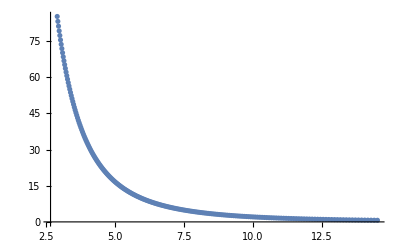

```mathematica
ListPlot[Table[{resset[[testip,1]],resset[[testip,2]]},{testip,1,npt}]]
```

### 4.2 Factor of Moment of inertia vs. mass

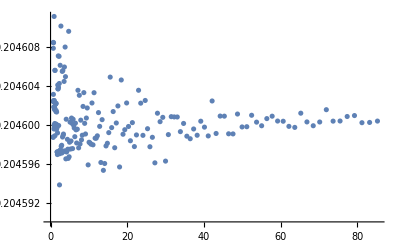

```mathematica
ListPlot[Table[{resset[[testip,2]],resset[[testip,3]]/(resset[[testip,2]]*(resset[[testip,1]])^2)},{testip,1,npt}]]
```

### 4.3 Tidal Love number vs. mass

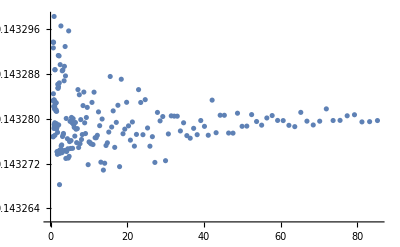

```mathematica
ListPlot[Table[{resset[[testip,2]],resset[[testip,4]]},{testip,1,npt}]]
```